```mathematica
κ=2π 6.85*^9/800
```

5.37998×10^7

```mathematica
g=2π 25*^6;
```

```mathematica
γ=κ g^2/(2π 500*^6)^2
```

134499.

```mathematica
1/γ 1*^9
```

7434.98

```mathematica
ps = Map[Block[{n=#},Sum[p(1-p)^(i-1),{i,1,n}]]&,Range[1,20]];
```

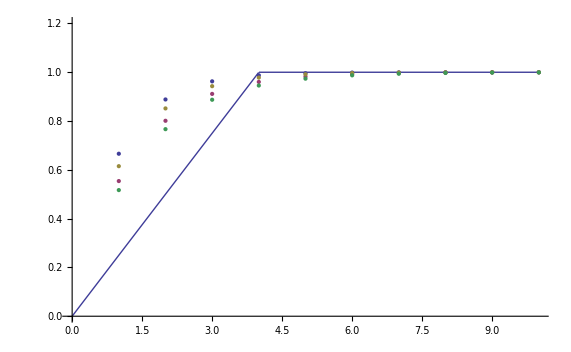

```mathematica
Show[Plot[Piecewise[{{x/4,x<4},{1,x≥4}}],{x,0,10},PlotRange->Full],ListPlot[{ps /.{p->0.666},ps /. {p->0.554},ps /. {p->0.615},ps /. {p->0.517}},PlotRange->Full],PlotRange->{{0,10},{0,1.2}}]
```

```mathematica
Export[NotebookDirectory[]<>"comparision_grover_classical.csv",{Map[Block[{x=#},Piecewise[{{x/4,x<4},{1,x≥4}}]]&,Range[1,20]],ps /.{p->0.666},ps /. {p->0.554},ps /. {p->0.615},ps /. {p->0.517}}]
```

{{1/4,1/2,3/4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0.666,0.888444,0.96274,0.987555,0.995843,0.998612,0.999536,0.999845,0.999948,0.999983,0.999994,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.},{0.554,0.801084,0.911283,0.960432,0.982353,0.992129,0.99649,0.998434,0.999302,0.999689,0.999861,0.999938,0.999972,0.999988,0.999995,0.999998,0.999999,1.,1.,1.},{0.615,0.851775,0.942933,0.978029,0.991541,0.996743,0.998746,0.999517,0.999814,0.999928,0.999972,0.999989,0.999996,0.999998,0.999999,1.,1.,1.,1.,1.},{0.517,0.766711,0.887321,0.945576,0.973713,0.987304,0.993868,0.997038,0.998569,0.999309,0.999666,0.999839,0.999922,0.999962,0.999982,0.999991,0.999996,0.999998,0.999999,1.}}

{1/4,1/2,3/4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}